```mathematica
SetDirectory[NotebookDirectory[]]
```

D:\tonnam_backup\Research_scratch\Tools\Scripts

```mathematica
(*Absorbing Markov Chain with 2 absorbing end states and 4 transition states*)
```

```mathematica
Q=({{0, 0.5, 0, 0}, {0.5, 0, 0.5, 0}, {0, 0.5, 0, 0.5}, {0, 0, 0.5, 0}});
```

```mathematica
R=({{0.5, 0}, {0, 0}, {0, 0}, {0, 0.5}});
```

```mathematica
I4=IdentityMatrix[4];
```

```mathematica
F=Inverse[I4-Q];
```

```mathematica
MatrixForm[I4-Q]
```

(1 | -0.5 | 0 | 0
-0.5 | 1 | -0.5 | 0
0 | -0.5 | 1 | -0.5
0 | 0 | -0.5 | 1)

```mathematica
Total[F]
```

{4.,6.,6.,4.}

```mathematica
MatrixForm[F]
```

(1.6 | 1.2 | 0.8 | 0.4
1.2 | 2.4 | 1.6 | 0.8
0.8 | 1.6 | 2.4 | 1.2
0.4 | 0.8 | 1.2 | 1.6)

```mathematica
MatrixForm[Total[F]]
```

(4.
6.
6.
4.)

```mathematica
MatrixForm[F.R]
```

(0.8 | 0.2
0.6 | 0.4
0.4 | 0.6
0.2 | 0.8)

```mathematica
n=9;
QMat=Append[(IdentityMatrix[n]/2)[[2;;-1]],Table[0,{n}]]+Join[{Table[0,{n}]},(IdentityMatrix[n]/2)[[1;;-2]]];
MatrixForm[QMat];
```

```mathematica
RMat=Join[{{0.5,0}},Table[{0,0},{n-2}],{{0,0.5}}];
MatrixForm[RMat];
```

```mathematica
IMat=IdentityMatrix[n];
MatrixForm[IMat];
```

```mathematica
FMat=Inverse[IMat-QMat];
```

```mathematica
MatrixForm[FMat];
```

```mathematica
MatrixForm[Total[FMat]];
```

```mathematica
MatrixForm[FMat.RMat]
```

(0.9 | 0.1
0.8 | 0.2
0.7 | 0.3
0.6 | 0.4
0.5 | 0.5
0.4 | 0.6
0.3 | 0.7
0.2 | 0.8
0.1 | 0.9)

```mathematica
calcpro[n_,zini_]:=
Module[{},
QMat=Append[(IdentityMatrix[n]/2)[[2;;-1]],Table[0,{n}]]+Join[{Table[0,{n}]},(IdentityMatrix[n]/2)[[1;;-2]]];
RMat=Join[{{0.5,0}},Table[{0,0},{n-2}],{{0,0.5}}];
IMat=IdentityMatrix[n];
FMat=Inverse[IMat-QMat];
(FMat.RMat)[[-(zini+1),2]]
];
```

```mathematica
(* Applying to Flux PMF Xin PVP10
z-absorb: Ag100 = 20.8625 Ang, Ag111 = 23.66875 Ang
  Difference = 2.80625 Ang
Divide difference into 50 states
1 Markov state = 0.056125 Ang
*)
```

```mathematica
zdiff=50;
```

```mathematica
(*ToBulk Vary
Set zini = 20 states above Ag111 absorbing state = 1.07 Ang
Xin rule out Ag as absorbed by bulk phase if it goes 15 Ang up away from the absorbing state
15 Ang = 280 states
*)
```

```mathematica
ToBulkList=Range[21,361,20];
pratio=Reap[
For[i=1,i≤Length[ToBulkList],i++,
proAg111=calcpro[ToBulkList[[i]],20];
proAg100=calcpro[zdiff+ToBulkList[[i]],20+zdiff];
Sow[N[proAg111/proAg100]];
]
][[2,1]];
```

```mathematica
pratio
```

{3.27273,2.19048,1.80645,1.60976,1.4902,1.40984,1.35211,1.30864,1.27473,1.24752,1.22523,1.20661,1.19084,1.1773,1.16556,1.15528,1.1462,1.13812}

```mathematica
ToBulkList[[14]]
```

281

```mathematica
pratio[[14]]
```

1.1773

```mathematica
ToBulkGraph=ListPlot[Partition[Riffle[Range[21,361,20]*0.0535,pratio],2],Frame->True,PlotLabel->"ToBulk propagation (z_ini = 1A above Ag111)",FrameLabel->{"ToBulk (Ang)","p-ratio"},LabelStyle->Directive[FontSize->15]]
```

$Aborted

```mathematica
CreateDirectory["graphs"];
Export["graphs/ToBulk-propagation.png",ToBulkGraph,ImageResolution->100];
```

CreateDirectory::filex: "D:\\tonnam_backup\\Research_scratch\\Tools\\Scripts\\graphs\\" already exists.

```mathematica
(*Vary z_ini
ToBulk=280
*)
```

```mathematica
ziniVary=Range[1,271,30];
pratio=Reap[
For[i=1,i≤Length[ziniVary],i++,
proAg111=calcpro[280,ziniVary[[i]]];
proAg100=calcpro[280+zdiff,ziniVary[[i]]+zdiff];
Sow[N[proAg111/proAg100]];
]
][[2,1]];
```

```mathematica
calcpro[280,1]
```

0.992883

```mathematica
calcpro[280+50,1+50]
```

0.8429

```mathematica
calcpro[280,1]/calcpro[280+50,1+50]
```

1.17794

```mathematica
calcpro[280,279]
```

0.00355872

```mathematica
calcpro[280+50,279+50]
```

0.00302115

```mathematica
calcpro[280,279]/calcpro[280+50,279+50]
```

1.17794

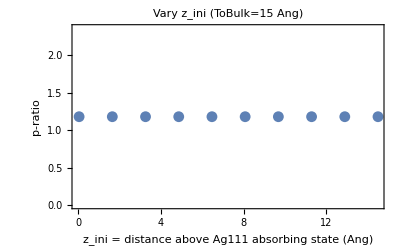

```mathematica
ziniGraph=ListPlot[Partition[Riffle[ziniVary*0.0535,pratio],2],Frame->True,
PlotLabel->"Vary z_ini (ToBulk=15 Ang)",FrameLabel->{"z_ini = distance above Ag111 absorbing state (Ang)","p-ratio"},PlotRange->All,LabelStyle->Directive[FontSize->15]]
```

```mathematica
Export["graphs/ziniGraph-Absorb.png",ziniGraph,ImageResolution->100]
```

graphs/ziniGraph-Absorb.png

```mathematica
Mean[pratio]
```

1.17794

```mathematica
(*Vary zdiff
ToBulk=280
zini=31
*)
```

```mathematica
zdiffVary=Range[1,201,20];
pratiozdiff=Reap[
For[i=1,i≤Length[zdiffVary],i++,
proAg111=calcpro[280,31];
proAg100=calcpro[280+zdiffVary[[i]],31+zdiffVary[[i]]];
Sow[N[proAg111/proAg100]];
]
][[2,1]];
```

```mathematica
pratiozdiff
```

{1.00356,1.07473,1.14591,1.21708,1.28826,1.35943,1.4306,1.50178,1.57295,1.64413,1.7153}

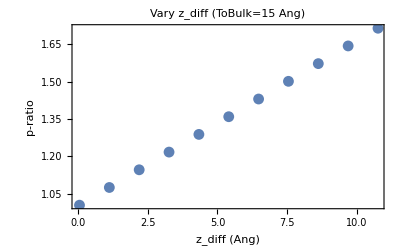

```mathematica
zdiffGraph=ListPlot[Partition[Riffle[zdiffVary*0.0535,pratiozdiff],2],Frame->True,
PlotLabel->"Vary z_diff (ToBulk=15 Ang)",FrameLabel->{"z_diff (Ang)","p-ratio"},PlotRange->All,LabelStyle->Directive[FontSize->15]]
```

```mathematica
Export["graphs/zdiffGraph-Absorb.png",zdiffGraph,ImageResolution->100]
```

graphs/zdiffGraph-Absorb.png

```mathematica
zdiff=50;
ToBulk=231;
zini=31;
```

```mathematica
proAg111=calcpro[ToBulk,31]
```

0.862069

```mathematica
proAg100=calcpro[ToBulk+zdiff,31+zdiff]
```

0.70922

```mathematica
proAg111/proAg100
```

1.21552

```mathematica
ToBulk*0.056125
```

12.9649